```mathematica
Clear["Global`*"]
```

Variables to Adjust

```mathematica
Coordinates :={43,-35,31,-23,13,-5,1}
```

END of Variables to Adjust

```mathematica
XMax := 20
```

```mathematica
XOffset:=0
```

```mathematica
SumOfBinomials[vector_,x_] := Sum[vector[[i+1]]*Binomial[x,i],{i,0,Length[vector]-1}]
```

```mathematica
ValuationInteger[p_,x_] :=If[!Divisible[x,p],0,ValuationInteger[p,x/p]+1]
```

```mathematica
ValuationRational[p_,x_] := If[Divisible[Numerator[x],p],ValuationInteger[p,Numerator[x]],-ValuationInteger[p,Denominator[x]]]
```

```mathematica
Poly[x_]=Expand[InterpolatingPolynomial[Table[SumOfBinomials[Coordinates,x+XOffset],{x,1,20}],x]]
```

43-(751 x)/12+(1594 x^2)/45-(425 x^3)/48+(155 x^4)/144-x^5/16+x^6/720

```mathematica
FixedPointPoly[x_] = Poly[x] - x
```

43-(763 x)/12+(1594 x^2)/45-(425 x^3)/48+(155 x^4)/144-x^5/16+x^6/720

```mathematica
NewtonPlot[p_,polynomial_]:=ListLinePlot[Table[ValuationRational[p,x],{x,CoefficientList[polynomial[x],{x}]}],AxesOrigin->{0,0},GridLines->{{},Range[-100,100]},PlotMarkers->All,DataRange->{0,Length[CoefficientList[polynomial[x],{x}]]-1},PlotLabel->"p = "<>ToString[p],PlotRange->All,AspectRatio->Automatic]
```

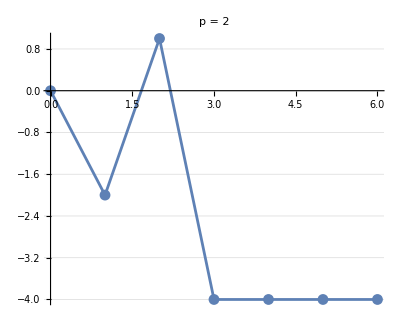

```mathematica
NewtonPlot[2,FixedPointPoly]
```